```mathematica
<<"C:\\Users\\LukinLab\\My Documents\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\SpectraFitting.m";
```

Usage Instructions:

1. Get a list of spectra from a directory by using the GetSpecDir[path] function.

2. (Optional) Get an individual spectrum for flatfield correction using the GetSpec[path] function. Divide each spectrum by this flat-field using the SpecDivide[spec,ffspec] function.

3. Initialize a list of guesses using the CoordInit[Spectra,center,d] function, where center is a very preliminary guess for the center point of a generic spectrum and d is the overall spread to zoom in on for further fitting. You should save this guess as a variable.

4. Use the PickGuesses[Spectra,CoordList] command to interactively refine these guesses. CoordList should be the variable you defined in the previous step.

5. Run SingleLorentzianFit[Spectra, Coordlist] to fit each function to a single Lorentzian. Save the output to a variable. More options are coming soon.

6. Use the ShowFits[Spectra, CoordList, Fits, Path] where Fits is the list of fits and Path is the original directory to display all of the fits and important parameters.


If you need additional help, all of the functions have usage instructions that can be queried with two question marks and the name of the function, e.g. ??ShowFits .

Location of XPS excel file.

```mathematica
XPSPath="C:\\Users\\LukinLab\\My Documents\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\Example Data\\XPS\\2014-06-17_10048_76_77_79_synchotronsamples.xlsx";
```

## Fitting Example Data

### Example 1: Sample carbon 1s edge

First, generate some fake data from example peak positions for a carbon 1s edge:

0.012 ⅇ^(-5.55556 (-2.3+x)^2)+0.012 ⅇ^(-5.55556 (-1.2+x)^2)+1.083 ⅇ^(-5.55556 x^2)+0.147 ⅇ^(-5.55556 (0.9+x)^2)+0.0333333 ⅇ^(-5.55556 (1.8+x)^2)

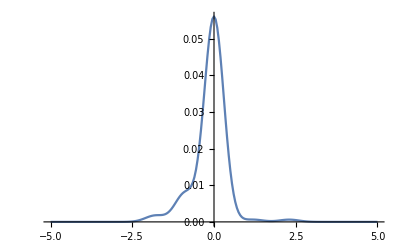

```mathematica
exweights={.10,.21,.57,.06,.06}^2; (*A^2 values, then plug in A values below*)
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[Sqrt[exweights[[i]]],expositions[[i]],0.3,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

Try to fit this data with default values. It does a pretty good job, but misses the distinction between the peak at 1.2 and 2.3 eV.

Sum of squares of residuals (as percent of total): 0.11848039866267279

Weight | μ | σ
5.42838×10^-6 | -8.89957 | 7.89326
0.424964 | -0.349339 | -0.351309
0.434476 | -0.345522 | 0.353717
0.0654851 | -8.30527 | 11.7618
0.0750687 | 7.56113 | -24.8363

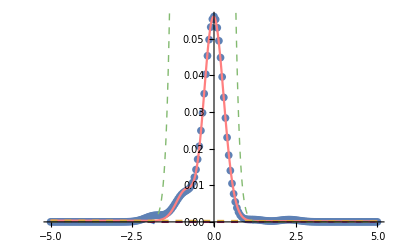

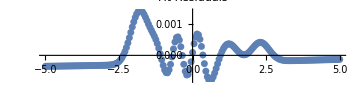

```mathematica
ExCModel=Model[ExampleCData,5];
FitSummary[ExampleCData,ExCModel];
```

Another option is to specify the method explicitly. The string gets passed directly to the NonLinearModelFit function.

Sum of squares of residuals (as percent of total): 0.01654682907399153

Weight | μ | σ
0.416414 | -0.12185 | -0.270808
0.0518079 | -0.905916 | 0.226622
0.165734 | -0.56689 | -0.938435
0.319295 | 0.0895519 | -0.236059
0.0467493 | 0.37998 | 0.185943

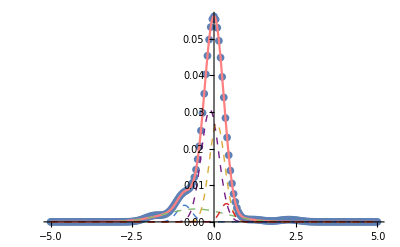

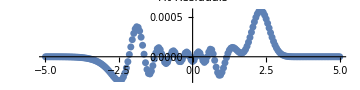

```mathematica
ExCModel=Model[ExampleCData,5,{},"g",0.75,0,"Method->NMinimize"];
FitSummary[ExampleCData,ExCModel];
```

We can also tweak the values on the default option to try to get an improvement:

Sum of squares of residuals (as percent of total): 0.017813463079003094

Weight | μ | σ
0.112822 | 0.222748 | 0.233671
4.5391×10^-10 | 0.127845 | 0.547523
0.0576401 | -0.886698 | 0.242338
0.671075 | -0.0391729 | 0.279761
0.158463 | -0.592537 | -0.936714

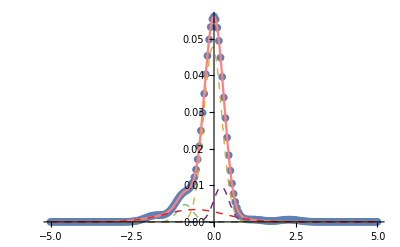

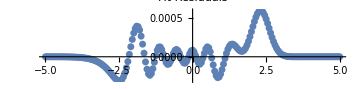

```mathematica
ExCModel=Model[ExampleCData,5,{},"g",0.75];
FitSummary[ExampleCData,ExCModel];
```

### Example 2: Sample carbon 1s edge with broader peaks

Broaden the peaks from example 1. The data appears to be much harder to fit!

0.0036 ⅇ^(-3.125 (-2.3+x)^2)+0.0036 ⅇ^(-3.125 (-1.2+x)^2)+0.3249 ⅇ^(-3.125 x^2)+0.0441 ⅇ^(-3.125 (0.9+x)^2)+0.01 ⅇ^(-3.125 (1.8+x)^2)

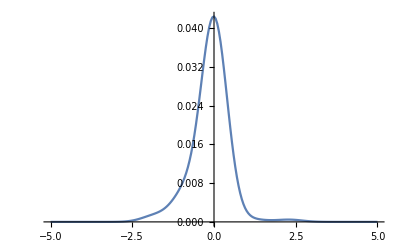

```mathematica
exweights={.10,.21,.57,.06,.06}^2; (*A^2 values, then plug in A values below*)
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[Sqrt[exweights[[i]]],expositions[[i]],0.4,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

Try to fit this data with default values. It does a pretty good job, but misses the distinction between the peak at 1.2 and 2.3 eV.

Sum of squares of residuals (as percent of total): 0.0003685377144117214

Weight | μ | σ
0.287103 | -0.450785 | -0.690352
0.00982583 | -1.98678 | -0.327446
0.00499809 | -1.0134 | 0.223801
0.68531 | 0.0163287 | 0.382365
0.0127638 | 2.12781 | -0.559788

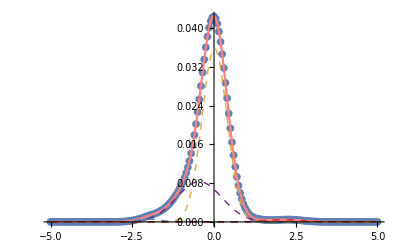

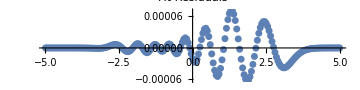

```mathematica
ExCModel=Model[ExampleCData,5];
FitSummary[ExampleCData,ExCModel];
```

Here again, decreasing the scaling factor (the default value is 0.95) produces a better fit that exactly reproduces the data.

Sum of squares of residuals (as percent of total): 0.00036853929541100846

Weight | μ | σ
0.685257 | 0.016338 | 0.382357
0.00498973 | -1.01361 | -0.223649
0.00983247 | -1.98668 | 0.327531
0.0127628 | 2.12763 | 0.559689
0.287158 | -0.450701 | 0.690301

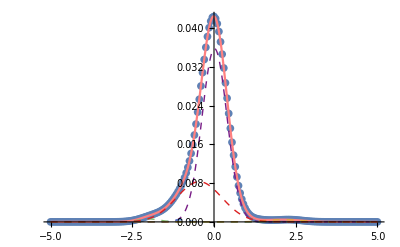

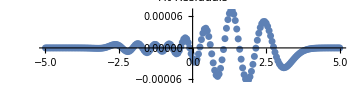

```mathematica
ExCModel=Model[ExampleCData,5,{},"g",.99];
FitSummary[ExampleCData,ExCModel];
```

### Example 3: Sample carbon 1s edge with narrower peaks

Make the peaks in example 1 more narrow.

0.0036 ⅇ^(-12.5 (-2.3+x)^2)+0.0036 ⅇ^(-12.5 (-1.2+x)^2)+0.3249 ⅇ^(-12.5 x^2)+0.0441 ⅇ^(-12.5 (0.9+x)^2)+0.01 ⅇ^(-12.5 (1.8+x)^2)

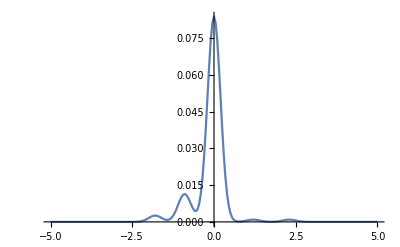

```mathematica
exweights={.10,.21,.57,.06,.06}^2; (*A^2 values, then plug in A values below*)
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[Sqrt[exweights[[i]]],expositions[[i]],0.2,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

Again, the default values do an OK job, but miss the higher energy peaks:

Sum of squares of residuals (as percent of total): 0.04985362373894116

Weight | μ | σ
0.698093 | -0.0268278 | -0.186075
1.08515×10^-9 | -0.389143 | -0.185129
0.0828793 | -0.89814 | 0.169263
0.11917 | 0.162388 | 0.158922
0.0998583 | -0.802406 | -1.03487

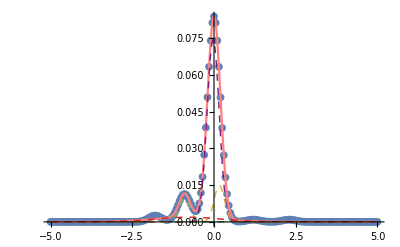

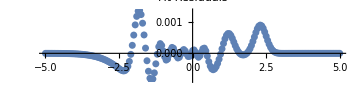

```mathematica
ExCModel=Model[ExampleCData,5,{},"g",0.95,0.0];
FitSummary[ExampleCData,ExCModel];
```

Again, decreasing the scaling factor a bit more gets precisely the correct result. Although it seems as if the choice of scaling factor should be more robust in this case, it does not appear to be.

Sum of squares of residuals (as percent of total): 2.9330313658654744e-12

Weight | μ | σ
0.0093216 | 1.2 | 0.200001
0.841274 | -8.13229×10^-9 | -0.2
0.0258933 | -1.8 | -0.2
0.00932164 | 2.3 | 0.200002
0.11419 | -0.9 | 0.2

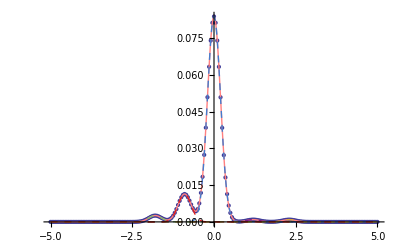

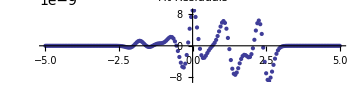

```mathematica
ExCModel=Model[ExampleCData,5,{},"g",0.65];
FitSummary[ExampleCData,ExCModel];
```

### Example 4: Sample carbon 1s edge plus noise

Generate the same data, but add some noise:

0.0036 ⅇ^(-5.55556 (-2.3+x)^2)+0.0036 ⅇ^(-5.55556 (-1.2+x)^2)+0.3249 ⅇ^(-5.55556 x^2)+0.0441 ⅇ^(-5.55556 (0.9+x)^2)+0.01 ⅇ^(-5.55556 (1.8+x)^2)

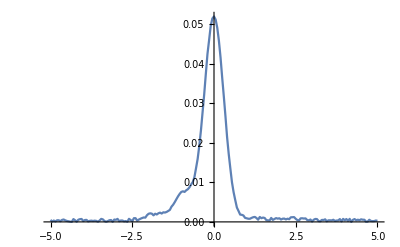

```mathematica
exweights={.10,.21,.57,.06,.06}^2; (*A^2 values, then plug in A values below*)
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[Sqrt[exweights[[i]]],expositions[[i]],0.3,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0.005*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

Fitting this data is more difficult. We can again reproduce the qualitative features fairly well. However, the higher energy peaks are lost and the lower energy peaks are mixed together.

Sum of squares of residuals (as percent of total): 0.1670885220180075

Weight | μ | σ
9.754×10^-10 | 0.0856776 | 0.399409
0.129658 | 0.210395 | -0.179317
0.494213 | -0.061202 | 0.238307
0.351893 | -0.438529 | 0.751132
0.0242363 | 0.450155 | 0.129027

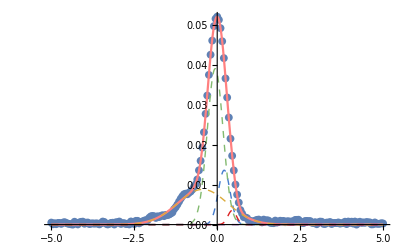

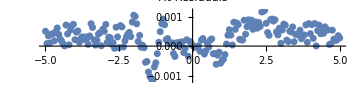

```mathematica
ExCModel=Model[ExampleCData,5];
FitSummary[ExampleCData,ExCModel];
```

Using the same parameters that were “good” before now yield obviously bad results. This parameter governs roughly how agressive the optimization should be in searching parameter space, so if it is too low it can fail to find obvious improvements.

Sum of squares of residuals (as percent of total): 0.0322123997892772

Weight | μ | σ
0.0210847 | 1.62671 | 0.998942
0.696178 | -0.000692201 | -0.299012
0.0203939 | -1.82208 | 0.272115
0.16602 | 1.06946 | -9.18804
0.0963237 | -0.916259 | 0.303745

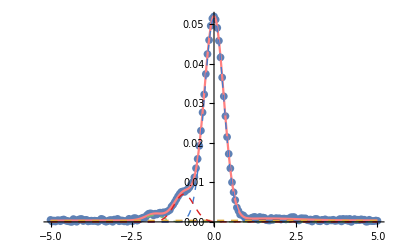

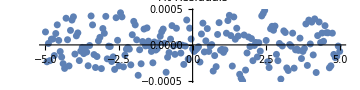

```mathematica
ExCModel=Model[ExampleCData,5,{},"g",0.75];
FitSummary[ExampleCData,ExCModel];
```

Increasing the scaling factor slightly does a good job of fitting the lower energy peaks, though the higher energy peaks are again lost in the noise.

Sum of squares of residuals (as percent of total): 0.057198471224545584

Weight | μ | σ
0.270483 | 0.204799 | 0.227389
0.0428837 | -0.330786 | 0.157057
0.319848 | -0.0701719 | 0.20592
0.226932 | -0.563019 | 0.562751
0.139854 | 0.183943 | 2.99974

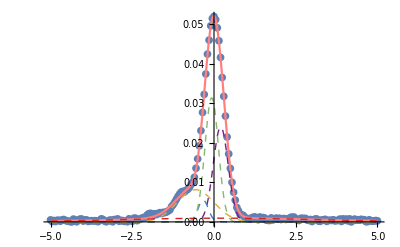

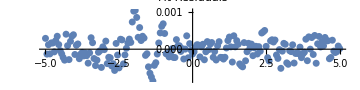

```mathematica
ExCModel=Model[ExampleCData,5,{},"g",0.9];
FitSummary[ExampleCData,ExCModel];
```

Increasing the amount of noise makes fitting even more challenging. Try it!

### Example 5: Sample carbon 1s edge plus noise using guessed peak locations

We can do better if we give a “guess” to the model function. All we have to do is pass a list of parameters instead of the number of peaks. See the usage instructions for Model:

```mathematica
?Model
```

Model[data,n] takes in a two-dimensional list data and a desired number of gaussians n and returns a nonlinear model for the data.
This is a difficult thing to do in general, so the function is tuned to fit the sort of data we usually get from the XPS. It works best if CenterAndNormalize has first been applied to the data. Sometimes additional tuning in the form of two optional arguments (the Scaling Factor sf and the Crossing Probability cp) can be helpful. See the complete argument list (type ??Model); many other optional parameters must also be specified in this case.
Instead of a desired number of gaussians, a list of guesses can be passed to the function in the format {{Prefactor 1, Mean 1, σ 1}, {Prefactor 2, Mean 2, σ 2}, ..., {Prefactor n, Mean n, σ n}}. In this case, the function will automatically detect that you're passing it a guess and start fitting around these parameters.
The third optional parameter is a three-argument list of bounds that gives the fractional variation to allow in each of the prefactors, means, and widths. 
The next optional parameter is a flag "g", "l", or "v" to pick gaussian, lorentzian, or voigt peaks to fit with.

```mathematica
exguess={exweights,expositions,0.3+0#&/@Range[5]}ᵀ
```

{{0.1,-1.8,0.3},{0.21,-0.9,0.3},{0.57,0,0.3},{0.06,1.2,0.3},{0.06,2.3,0.3}}

We can get a substantial improvement over the non-guessed list:

Sum of squares of residuals (as percent of total): 7.900848380044095e-10

Weight | μ | σ
0.025894 | -1.79999 | 0.300007
0.114189 | -0.899998 | 0.299998
0.841274 | -1.75358×10^-7 | 0.3
0.00932354 | 1.20009 | 0.30009
0.00931997 | 2.30009 | 0.299924

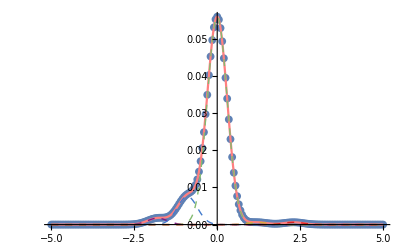

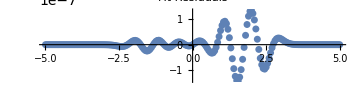

```mathematica
ExCModel=Model[ExampleCData,exguess];
FitSummary[ExampleCData,ExCModel];
```

### Example 6: Sample carbon 1s edge plus noise, using known peak locations

We saw before that fitting with noise was a bit challenging. Let’s look at that data again:

0.0036 ⅇ^(-5.55556 (-2.3+x)^2)+0.0036 ⅇ^(-5.55556 (-1.2+x)^2)+0.3249 ⅇ^(-5.55556 x^2)+0.0441 ⅇ^(-5.55556 (0.9+x)^2)+0.01 ⅇ^(-5.55556 (1.8+x)^2)

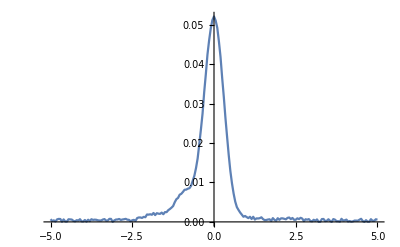

```mathematica
exweights={.10,.21,.57,.06,.06}^2; (*A^2 values, then plug in A values below*)
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[Sqrt[exweights[[i]]],expositions[[i]],0.3,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0.005*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

Instead of fitting the data with completely free parameters, we can use known (or suspected) positions of the peaks using the FixedPeaksModel command (note also the change in syntax of FitSummary). The default parameters do an abysmal job:

Sum of squares of residuals (as percent of total): 0.22180123299554624

Using fixed peaks analysis methods. μ -> -2.30396

Weight | σ
0.60855 | -57.1744
4.02507×10^-15 | -1.42602
0.00254571 | -0.279094
0.0489334 | -0.403607
0.339971 | 0.307102

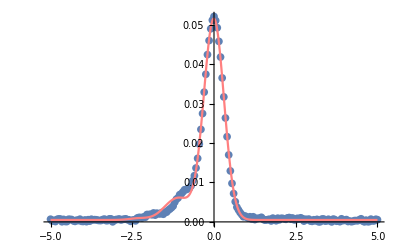

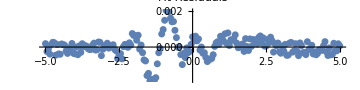

```mathematica
ExCModel=FixedPeaksModel[ExampleCData,expositions];
FitSummary[ExampleCData,ExCModel,"g",True];
```

Again, reducing the scaling factor makes all the difference, although the high-energy peaks are still lost in the noise.

Sum of squares of residuals (as percent of total): 0.03942058185505022

Using fixed peaks analysis methods. μ -> -0.000937745

Weight | σ
0.0190737 | -0.300052
0.0860876 | -0.30252
0.635634 | -0.29942
0.00624521 | 0.290387
0.25296 | 12.5433

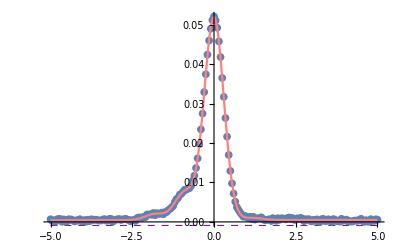

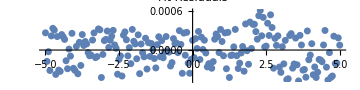

```mathematica
ExCModel=FixedPeaksModel[ExampleCData,expositions,0.6];
FitSummary[ExampleCData,ExCModel,"g",True];
```

This result is somewhat robust against perturbations in the peak positions (in case we guess wrong). Here we change the peak positions by a random amount up to 10%. (Pushing this up to 20% makes the fit obviously bad in some cases.)

Sum of squares of residuals (as percent of total): 0.24959779043602862

Using fixed peaks analysis methods. μ -> -2.27046

Weight | σ
0.0181294 | 0.812191
0.00404257 | 0.272292
0.0189929 | 0.334762
0.129269 | 0.387354
0.829566 | 0.308384

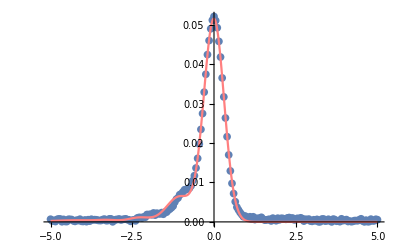

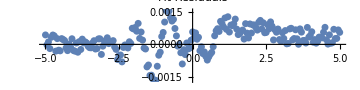

Sum of squares of residuals (as percent of total): 0.06658343432266084

Using fixed peaks analysis methods. μ -> 0.00961663

Weight | σ
0.0835485 | 1.95934
0.128122 | 0.421656
0.707126 | -0.290582
0.0179109 | 0.00322613
0.0632927 | -2.31503

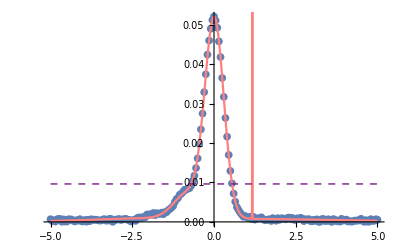

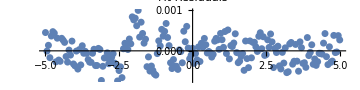

Sum of squares of residuals (as percent of total): 0.09012684138577359

Using fixed peaks analysis methods. μ -> 0.936674

Weight | σ
0.113243 | -0.375341
0.723157 | 0.297091
0.1636 | -4.5217
3.33321×10^-13 | 13.0963
2.47733×10^-14 | 6.20266

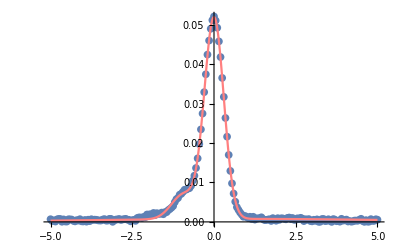

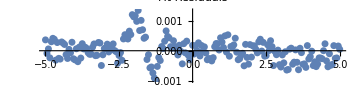

Sum of squares of residuals (as percent of total): 0.12949143691647158

Using fixed peaks analysis methods. μ -> 0.901008

Weight | σ
0.00216333 | -0.3707
0.0148862 | 0.30169
0.000779134 | 2.15076
0.982171 | 2537.91
6.32141×10^-17 | 0.761786

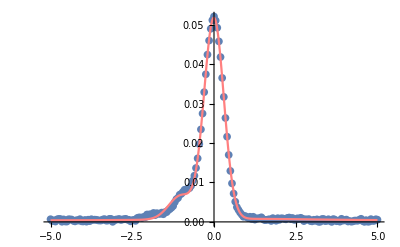

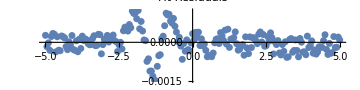

Sum of squares of residuals (as percent of total): 0.07773805020325379

Using fixed peaks analysis methods. μ -> 0.926491

Weight | σ
0.0556163 | 0.506656
0.238675 | -0.289203
0.00791529 | -1.06456
5.4636×10^-15 | 2.03715
0.697793 | -88.0201

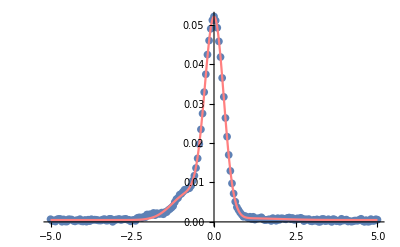

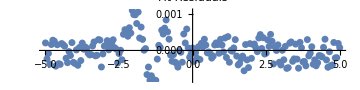

{Null,Null,Null,Null,Null}

```mathematica
Table[
ExCModel=FixedPeaksModel[ExampleCData,(#*RandomReal[{0.9,1.1}])&/@expositions,0.6];
FitSummary[ExampleCData,ExCModel,"g",True];
,{i,1,5}
]
```

### Example 7: Sample carbon 1s edge using constraints

One other option available is to use constraints. This forces the fitted values to be somewhat near the options that you have chosen, but they can vary by an amount that you choose. All the options are fractional except for the peak position, which is in real units.

```mathematica
exweights={.10,.21,.57,.06,.06}^2; (*A^2 values, then plug in A values below*)
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[Sqrt[exweights[[i]]],expositions[[i]],0.3,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0.005*0*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

0.0036 ⅇ^(-5.55556 (-2.3+x)^2)+0.0036 ⅇ^(-5.55556 (-1.2+x)^2)+0.3249 ⅇ^(-5.55556 x^2)+0.0441 ⅇ^(-5.55556 (0.9+x)^2)+0.01 ⅇ^(-5.55556 (1.8+x)^2)

-Graphics-

We specify the fit command as before, but we specify the constraints in the third argument. The value to beat in the sum of square is 0.015.

Unsurprisingly, if we use the correct guesses we get the correct answer.

FittedModel[0.000619796 ⅇ^(-5.55562 (-2.3+«13»)^2)+0.000619793 ⅇ^(-5.55537 «1»)+«1»+0.00759251 «1»+0.00172165 ⅇ^(-5.5556 («1»)^2)]

Sum of squares of residuals (as percent of total): 5.4407847334187e-12

Weight | μ | σ
0.0258931 | -1.8 | 0.299999
0.11419 | -0.899999 | 0.300001
0.841273 | 9.03358×10^-8 | 0.3
0.00932187 | 1.2 | 0.300005
0.00932149 | 2.3 | 0.299998

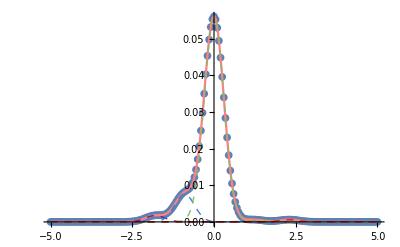

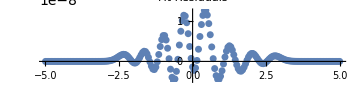

```mathematica
exguess={Sqrt[exweights]*0.3,expositions,0.3+0#&/@Range[5]}ᵀ;
ExCModel=Model[ExampleCData,exguess,{.3,0.1,0.1},"g",0.95,0]
FitSummary[ExampleCData,ExCModel,"g"];
```

This result is more robust against perturbations in the peak positions (in case we guess wrong):

```mathematica
RoughGuess:={Sqrt[exweights],expositions+0.05*RandomReal[{-1,1}],0.3+0.1*RandomReal[{-1,1}]+0*#&/@Range[5]}ᵀ;
```

```mathematica
Table[
ExCModel=Model[ExampleCData,RoughGuess,{.99,0.2,0.2},"g",0.95,0];
FitSummary[ExampleCData,ExCModel,"g",False,False];
,{i,1,5}
]
```

Sum of squares of residuals (as percent of total): 0.0000335589958981414

Weight | μ | σ
0.0261334 | -1.79836 | 0.301186
0.113443 | -0.900503 | 0.299028
0.842458 | -0.0000377203 | 0.300189
0.00792129 | 1.19759 | 0.271392
0.0100436 | 2.28998 | 0.312891

Sum of squares of residuals (as percent of total): 0.00017909911125667277

Weight | μ | σ
0.0263757 | -1.79342 | 0.301519
0.112447 | -0.901095 | 0.297397
0.845268 | -0.000144952 | 0.300402
0.00723687 | 1.21185 | 0.254566
0.00867319 | 2.29216 | 0.283291

Sum of squares of residuals (as percent of total): 9.189676616078998e-6

Weight | μ | σ
0.0254801 | -1.80212 | 0.297582
0.114982 | -0.899816 | 0.301002
0.840552 | 0.0000434069 | 0.299863
0.0100411 | 1.19599 | 0.31401
0.00894491 | 2.30034 | 0.292816

Sum of squares of residuals (as percent of total): 0.07131700211782972

Weight | μ | σ
0.0282043 | -1.78477 | 0.319746
0.203097 | -0.751664 | 0.373432
0.74418 | 0.014823 | 0.279554
0.0133455 | 1.00962 | 0.280304
0.0111733 | 2.28314 | 0.328115

Sum of squares of residuals (as percent of total): 0.0008113458137626358

Weight | μ | σ
0.0174893 | -1.83523 | 0.242324
0.126191 | -0.903325 | 0.315668
0.837391 | 0.000920953 | 0.299258
0.00997738 | 1.19767 | 0.311064
0.00895163 | 2.30257 | 0.292827

{Null,Null,Null,Null,Null}

## Bulk fitting of actual XPS data

### General i/o

List of samples

```mathematica
SampleList={00114,00113,00118,00117,00116,00115,10079,00119,10077,00019,10048};
```

Label by good/bad/other

```mathematica
StyleList={Red,Red,Blue,Blue,Red,Green,Green,Blue,Green,Blue,Green};
```

Literature peak positions (from above)

```mathematica
expositions={-1.8,-0.9,0,1.2,2.3};
```

### Carbon Peak

#### Setup

Use the GetSpec command to import the spectra from an excel file, keeping only the sheets containing the string specified in the third argument.

```mathematica
RawCData=GetSpec[XPSPath,"Excel XPS","C1s"];
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

11 spectra in all.

Importing Sheet C1s Scan J

Importing Sheet C1s Scan I

Importing Sheet C1s Scan H

Importing Sheet C1s Scan G

Importing Sheet C1s Scan F

Importing Sheet C1s Scan E

Importing Sheet C1s Scan D

Importing Sheet C1s Scan C

Importing Sheet C1s Scan B

Importing Sheet C1s Scan A

Importing Sheet C1s Scan

Formatting XPS Spectra

```mathematica
CSheets=GetSheets[XPSPath,"C1s"]
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

11 spectra in all.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

```mathematica
Ccoordlist=CoordInit[RawCData,285,8];
```

I have already picked some values. They can be manipulated further by the PickGuesses command.

```mathematica
Ccoordlist={{{285,1000},{282.22999999999996,2600.},{289.59999999999997,2750.},{289.38,3250.}},{{285,1000},{282.71999999999997,2300.},{290.22999999999996,3900.},{283.03999999999996,2700.}},{{285,1000},{282.93,3000.},{290.08,2650.},{289.76,3200.}},{{285,1000},{283.15,2850.},{290.43,2450.},{289.99,2750.}},{{285,1000},{282.12,2550.},{289.94,2600.},{289.53999999999996,3200.}},{{285,1000},{282.7,3250.},{289.84999999999997,3150.},{289.45,3250.}},{{285,1000},{282.7,2350.},{290.26,2550.},{283.06,2550.}},{{285,1000},{282.65999999999997,2450.},{290.47999999999996,2350.},{290.03,3000.}},{{285,1000},{283.2,2650.},{290.61,2450.},{290.26,3000.}},{{285,1000},{282.47999999999996,1750.},{290.08,2800.},{282.93,2450.}},{{285,1000},{283.11,3000.},{290.47999999999996,3200.},{290.12,4000.}}};
```

```mathematica
PickGuesses[RawCData,Ccoordlist]
```

{,,,,,,,,,,}

```mathematica
CData=UserRemoveAve[RawCData,Ccoordlist];
```

```mathematica
CenteredCData=CenterAndNormalize/@CData;
```

#### Fitting with free parameters

Run the model command over every element in the list of data

```mathematica
AllCModels=Model[#,5,"g",0.4]&/@CenteredCData;
```

The FitSummary command is very useful for viewing the results:

```mathematica
?FitSummary
```

FitSummary takes in the data from the original fit and the nonlinear model that you fit to this data, and outputs some summary information and plots. Fitsummary returns the table of data it prints out during processing.
Optional arguments are a boolean fixedpeaks which tells the function whether or not the model was generated with the FixedPeaksModel function.
The last optional argument plot tells the function whether or not to generate plots or just tables of statistical data.

Sum of squares of residuals (as percent of total): 0.005208741758023443

Weight | μ | σ
5.73396×10^-16 | -0.292864 | 0.334547
0.357487 | -0.0688682 | -0.608486
0.111965 | 0.950711 | 1.26734
4.83559×10^-14 | -0.216691 | 0.301545
0.530548 | 0.0418675 | -0.325906

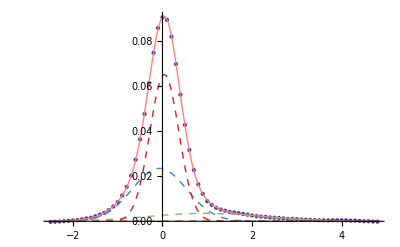

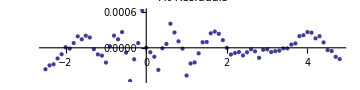

Sum of squares of residuals (as percent of total): 0.005666323276729629

Weight | μ | σ
0.112078 | -1.46934 | 0.609144
0.000536925 | -0.030086 | -0.00404935
0.347642 | 0.0169114 | 0.508166
0.388001 | -0.0174993 | -0.313576
0.151742 | 1.18443 | 1.40343

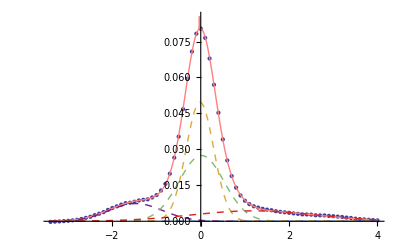

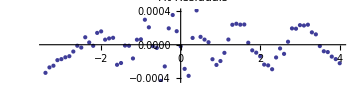

Sum of squares of residuals (as percent of total): 0.06720718179000186

Weight | μ | σ
0.65765 | 0.0201102 | 0.317268
0.34235 | -0.0731677 | -1.00883
5.83706×10^-14 | 0.346389 | 0.474119
5.81759×10^-14 | 0.225509 | 0.580842
2.18766×10^-15 | -0.323702 | -0.230181

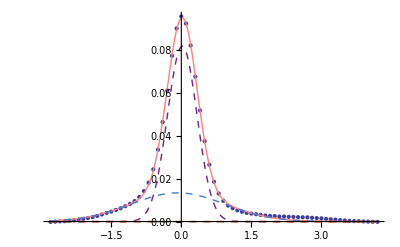

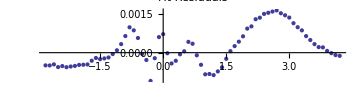

Sum of squares of residuals (as percent of total): 0.0023445273704215605

Weight | μ | σ
0.302569 | -0.12583 | -0.898263
0.0369027 | 2.31704 | -0.671876
1.47547×10^-10 | -0.459054 | -1.37542
0.614442 | -0.00605094 | 0.336641
0.0460864 | -0.0491268 | -0.206183

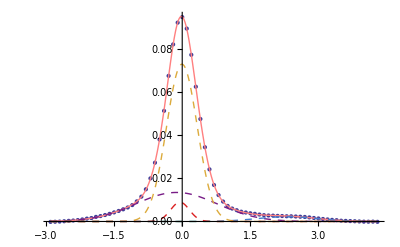

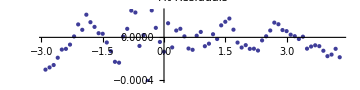

Sum of squares of residuals (as percent of total): 0.0035269873103849782

Weight | μ | σ
0.322761 | -0.187083 | -0.625005
5.84977×10^-10 | -0.0249256 | -1.1412
0.514779 | -0.00975151 | 0.345094
0.120462 | 0.922464 | 1.28376
0.0419972 | -0.0471548 | -0.216095

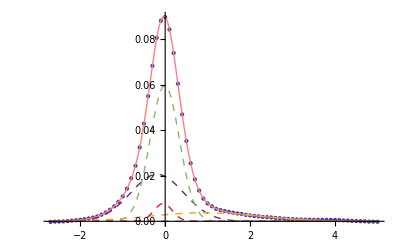

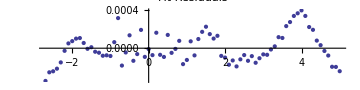

Sum of squares of residuals (as percent of total): 0.0008798250103409808

Weight | μ | σ
0.195054 | 0.050808 | 0.263325
0.06207 | 1.33654 | -0.922595
0.413262 | 0.0575123 | 0.37211
0.00338733 | 3.20528 | 0.418432
0.326226 | -0.315069 | -0.736469

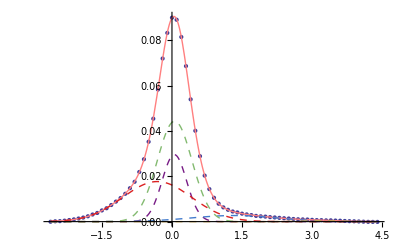

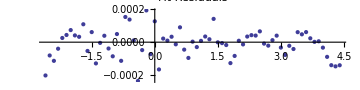

Sum of squares of residuals (as percent of total): 0.001129409683305237

Weight | μ | σ
0.0119057 | -1.74792 | 0.40119
0.569299 | 0.0157227 | -0.315764
0.0179347 | 0.504934 | 0.22248
0.0482417 | 2.31893 | 0.776683
0.352619 | -0.146819 | -0.854876

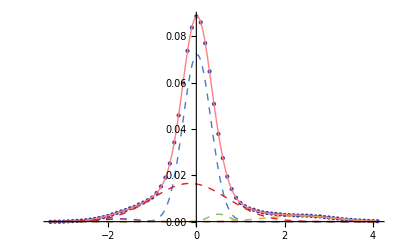

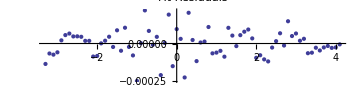

Sum of squares of residuals (as percent of total): 0.00370923814189739

Weight | μ | σ
2.03325×10^-9 | -0.212411 | 0.519393
0.525901 | 0.0470459 | 0.304779
0.348757 | 0.0313431 | -0.584969
0.0561554 | -1.26455 | -0.550741
0.0691856 | 1.8705 | 0.932152

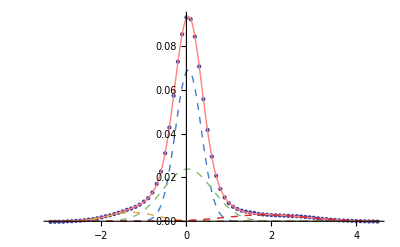

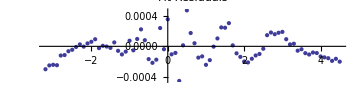

Sum of squares of residuals (as percent of total): 0.0025217484830287206

Weight | μ | σ
0.613217 | -0.0365067 | 0.324062
0.338939 | -0.207747 | 0.94578
0.0127581 | 0.540126 | -0.203455
3.47851×10^-8 | -0.30102 | -1.14235
0.0350859 | 2.38466 | 0.652374

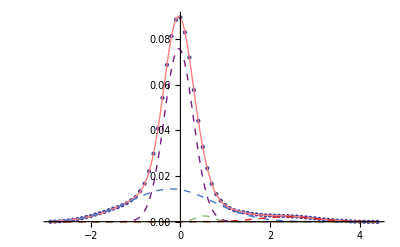

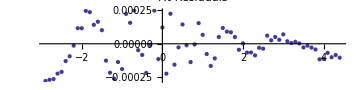

Sum of squares of residuals (as percent of total): 0.0010673273662961038

Weight | μ | σ
0.0650475 | 0.011936 | 0.229255
0.0524514 | 2.26596 | -0.83217
0.308552 | -0.105819 | 0.847912
0.563947 | 0.0585046 | 0.336843
0.0100018 | -1.74534 | -0.41184

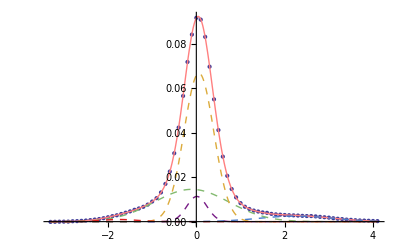

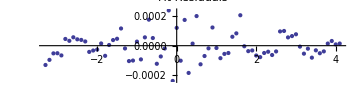

Sum of squares of residuals (as percent of total): 0.017824059065850967

Weight | μ | σ
0.294977 | 0.0593688 | -0.316744
0.323172 | -0.143492 | -1.3055
4.36632×10^-12 | 0.56078 | 0.779002
6.53268×10^-13 | 0.733016 | 0.579905
0.381851 | -0.00564224 | -0.411974

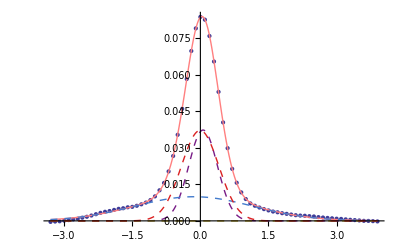

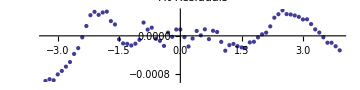

```mathematica
CSummaries=Table[FitSummary[CenteredCData[[x]],AllCModels[[x]]],{x,1,Length@CenteredCData}];
```

Visualize location of peaks and weights:

```mathematica
?ComparePeaks
```

ComparePeaks shows a plot of locations of the peaks in each spectrum labeled by the last symbol in the second argument. Typically, the second argument is the list of sheets, so the last letter is unique.
In the case of output from the FixedPeaksModel, the peak positions used in the model and the list of models themselves must also be included as arguments (in that order.)

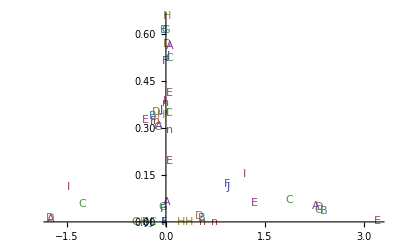

```mathematica
FreePeaks=ComparePeaks[CSummaries,CSheets];
```

#### Fitting with free parameters, starting with informed guesses.

Recall that Model can also be passed a list of guesses for peak amplitudes, locations, and sigmas instead of just a numerical value for the list of peaks. See the usage notes:

```mathematica
?Model
```

Model[data,n] takes in a two-dimensional list data and a desired number of gaussians n and returns a nonlinear model for the data.
This is a difficult thing to do in general, so the function is tuned to fit the sort of data we usually get from the XPS. It works best if CenterAndNormalize has first been applied to the data. Sometimes additional tuning in the form of two optional arguments (the Scaling Factor sf and the Crossing Probability cp) can be helpful. See the complete argument list (type ??Model); many other optional parameters must also be specified in this case.
Instead of a desired number of gaussians, a list of guesses can be passed to the function in the format {{Prefactor 1, Mean 1, σ 1}, {Prefactor 2, Mean 2, σ 2}, ..., {Prefactor n, Mean n, σ n}}. In this case, the function will automatically detect that you're passing it a guess and start fitting around these parameters.
The next optional parameter is a flag "g", "l", or "v" to pick gaussian, lorentzian, or voigt peaks to fit with.

```mathematica
expositions
```

{-1.8,-0.9,0,1.2,2.3}

```mathematica
guesses={{0.1,-1.8,0.5},{0.1,-0.9,0.5},{0.25,0,0.5},{0.05,1.2,0.5},{0.05,2.3,0.5}};
```

```mathematica
AllCModels=Model[#,guesses,"g",0.3,0.1]&/@CenteredCData;
```

Sum of squares of residuals (as percent of total): 0.00311301299340995

Weight | μ | σ
0.119086 | 0.916866 | 1.21261
0.308978 | -0.113738 | -0.609026
0.530232 | 0.0520241 | 0.345851
0.0417029 | -0.0066926 | 0.223992
6.36492×10^-9 | -0.860093 | 0.366104

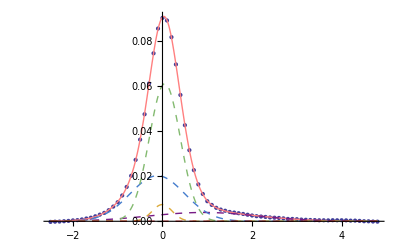

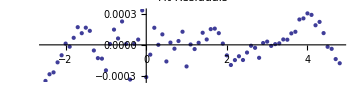

Sum of squares of residuals (as percent of total): 0.00566632610800518

Weight | μ | σ
0.112116 | -1.46947 | 0.60908
0.000163198 | -0.0618558 | 0.00388854
0.388299 | -0.0174863 | -0.313597
0.347692 | 0.0168859 | -0.508297
0.151729 | 1.18515 | 1.40321

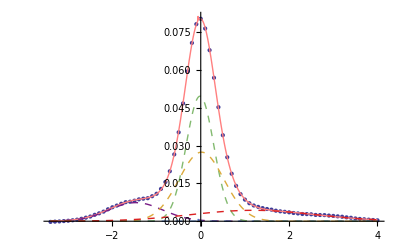

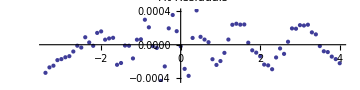

Sum of squares of residuals (as percent of total): 0.0017859751815677276

Weight | μ | σ
0.0213193 | 2.65382 | 0.548848
0.574459 | 0.0369781 | 0.347823
0.163807 | -0.582918 | -0.75176
0.131605 | 0.555132 | -0.929464
0.108808 | -0.00514581 | 0.231944

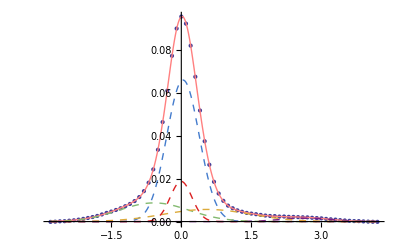

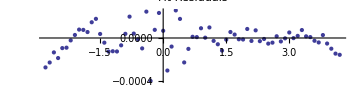

Sum of squares of residuals (as percent of total): 0.002344527033291141

Weight | μ | σ
0.614422 | -0.00604957 | 0.336649
9.94044×10^-10 | 0.0781294 | 0.399088
0.302557 | -0.125842 | -0.898277
0.0461174 | -0.0491123 | -0.20621
0.0369039 | 2.31702 | 0.671911

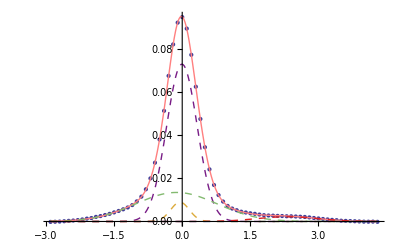

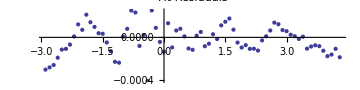

Sum of squares of residuals (as percent of total): 0.0016374990682454806

Weight | μ | σ
0.00454794 | 3.81556 | 0.382789
0.0796444 | -0.0403787 | 0.2379
0.509994 | -0.00585789 | -0.360306
0.283119 | -0.237508 | -0.627009
0.122694 | 0.881752 | 1.17039

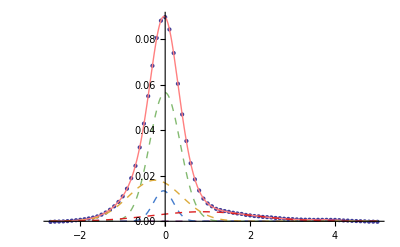

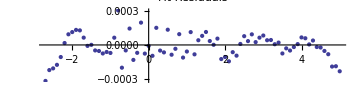

Sum of squares of residuals (as percent of total): 0.002438597426491393

Weight | μ | σ
0.0368845 | 1.94225 | 0.848523
0.00364204 | -0.637217 | 0.13086
0.551976 | 0.0520938 | -0.315031
2.1048×10^-11 | 0.0195086 | 1.33377
0.407498 | -0.182432 | 0.768364

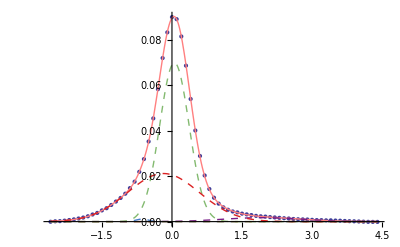

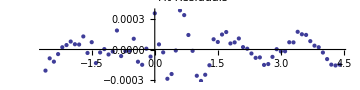

Sum of squares of residuals (as percent of total): 0.006416412747571962

Weight | μ | σ
6.83091×10^-12 | -0.366962 | 0.390016
0.356174 | -0.149653 | 0.978117
0.0352734 | 2.5359 | -0.637195
1.05799×10^-10 | 0.381797 | 1.14943
0.608553 | 0.023758 | 0.328952

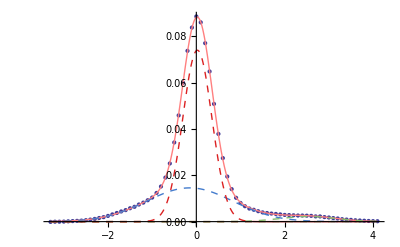

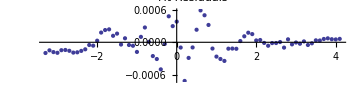

Sum of squares of residuals (as percent of total): 0.0018629774680024784

Weight | μ | σ
0.416219 | 0.040799 | 0.290062
0.0920181 | -1.01376 | 0.626834
0.426068 | 0.0862463 | -0.486799
0.023804 | 1.36426 | 0.367366
0.0418909 | 2.34554 | 0.676502

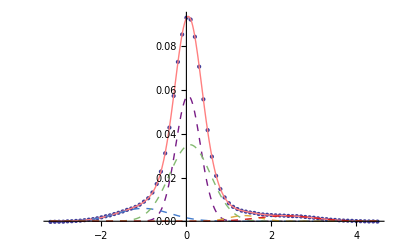

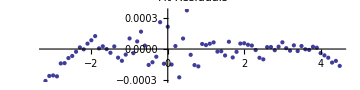

Sum of squares of residuals (as percent of total): 0.002358185940622013

Weight | μ | σ
0.61187 | -0.0367271 | -0.323778
0.0125827 | 0.53682 | 0.203965
0.00267353 | 1.70394 | -0.25875
0.0308331 | 2.47874 | -0.584875
0.342041 | -0.199904 | 0.947711

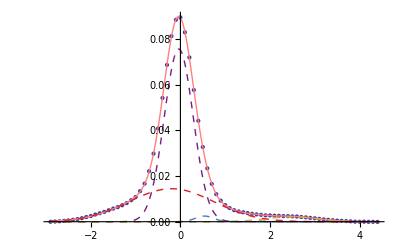

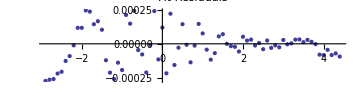

Sum of squares of residuals (as percent of total): 0.0014008666718087015

Weight | μ | σ
0.202585 | 0.0344698 | 0.26423
0.159196 | -0.588745 | 0.82251
0.122677 | 0.62232 | 0.955572
0.0301416 | 2.62668 | -0.665416
0.4854 | 0.062231 | 0.373941

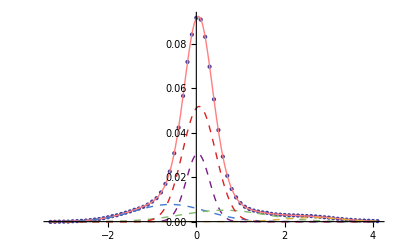

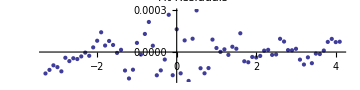

Sum of squares of residuals (as percent of total): 0.0020191074049039745

Weight | μ | σ
0.327286 | -0.0732026 | 0.915772
0.0272144 | 2.1937 | 0.665845
0.609259 | 0.034732 | -0.349068
0.0290439 | -1.95646 | -0.436852
0.00719758 | -0.691146 | 0.217391

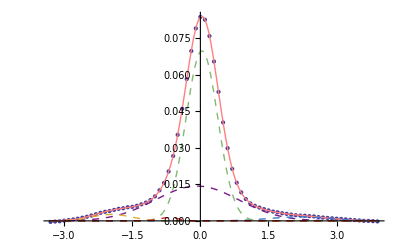

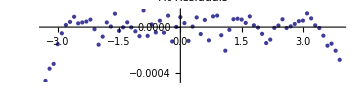

```mathematica
CSummaries=Table[FitSummary[CenteredCData[[x]],AllCModels[[x]]],{x,1,Length[CenteredCData],1}];
```

Visualize location of peaks and weights:

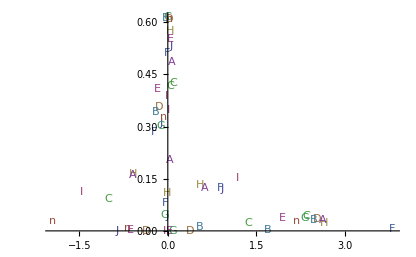

```mathematica
HintPeaks=ComparePeaks[CSummaries,CSheets];
```

#### Fitting with fixed peak positions

Recall our literature peak positions:

```mathematica
expositions
```

{-1.8,-0.9,0,1.2,2.3}

Now we’ll fit keeping the relative positions between the peaks fixed.

```mathematica
AllCModels=FixedPeaksModel[#,{-1.7,-0.9,0,1.2,2.5},0.45]&/@CenteredCData;
```

Note the syntax change in the FitSummary command:

Sum of squares of residuals (as percent of total): 0.013364391375841965

Using fixed peaks analysis methods. μ -> 0.9364

Weight | σ
0.0927976 | 0.418136
0.794355 | -0.360659
0.0811208 | -0.481871
0.0234726 | 0.461701
0.00825353 | -0.590615

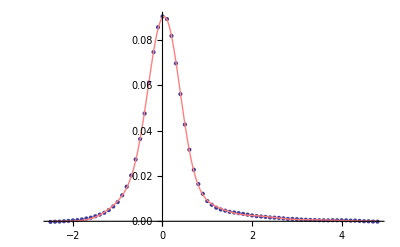

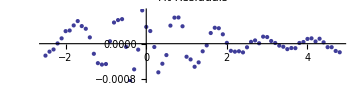

Sum of squares of residuals (as percent of total): 0.04803775436757973

Using fixed peaks analysis methods.                 -6
μ -> -3.60626 10

Weight | σ
0.0166737 | -0.402568
0.188459 | 0.913666
0.647814 | -0.362148
0.0888785 | -0.805099
0.0581753 | 1.88623

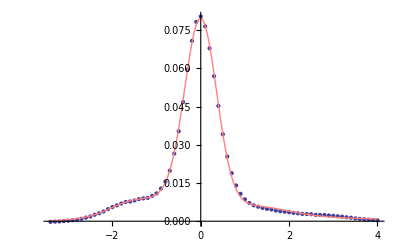

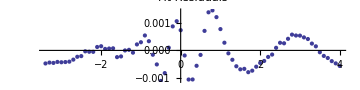

Sum of squares of residuals (as percent of total): 0.052702625241888366

Using fixed peaks analysis methods. μ -> 0.0239424

Weight | σ
0.0262096 | -0.355799
0.0756446 | 0.345696
0.807922 | -0.343303
0.069144 | -0.510867
0.0210798 | 0.417827

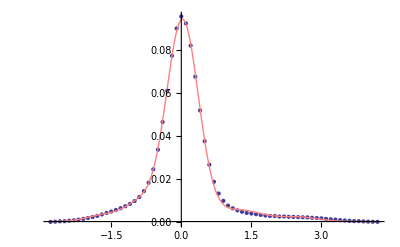

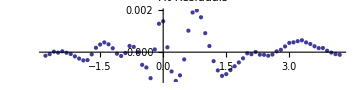

Sum of squares of residuals (as percent of total): 0.044900432691312095

Using fixed peaks analysis methods. μ -> -0.0119081

Weight | σ
0.0244001 | 0.362221
0.0621946 | 0.32536
0.818795 | -0.349513
0.0715629 | -0.516028
0.0230473 | 0.411073

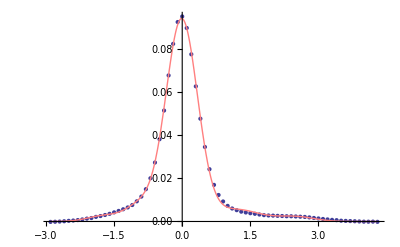

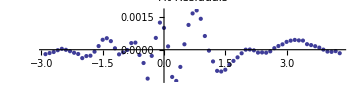

Sum of squares of residuals (as percent of total): 0.0392408540206525

Using fixed peaks analysis methods. μ -> -0.0237482

Weight | σ
0.000611808 | -0.00290965
0.0804325 | 0.384597
0.819853 | -0.373149
0.0686298 | -0.550968
0.0304733 | 1.17296

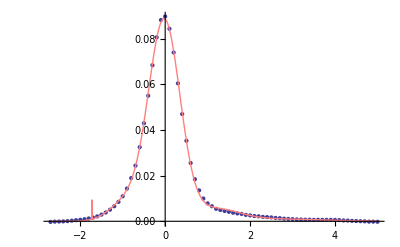

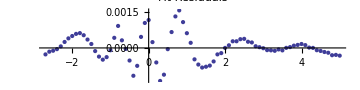

Sum of squares of residuals (as percent of total): 0.03689127331940348

Using fixed peaks analysis methods. μ -> 0.044267

Weight | σ
0.0207483 | -0.316359
0.107784 | 0.35022
0.796104 | -0.357438
0.0627784 | -0.503698
0.0125859 | 0.415244

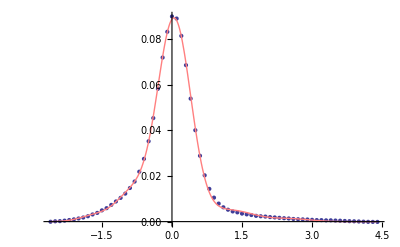

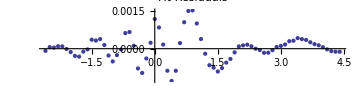

Sum of squares of residuals (as percent of total): 0.04176721831158928

Using fixed peaks analysis methods. μ -> 0.0260135

Weight | σ
0.0384405 | 0.435177
0.0811938 | -0.388509
0.781905 | -0.358683
0.0693825 | -0.497847
0.029078 | -0.471291

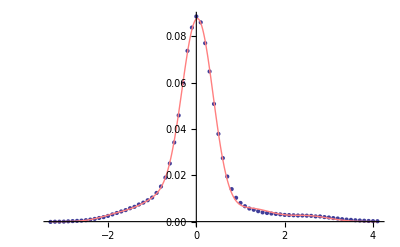

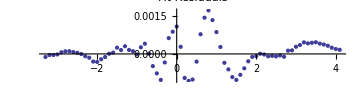

Sum of squares of residuals (as percent of total): 0.05047505926094115

Using fixed peaks analysis methods. μ -> 0.0470849

Weight | σ
0.028572 | -0.374952
0.0652945 | 0.341164
0.780533 | -0.346744
0.1256 | 1.02675
2.11711×10^-13 | 1.35151

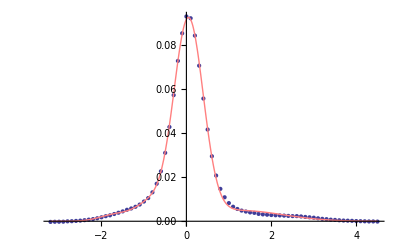

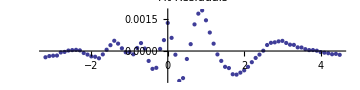

Sum of squares of residuals (as percent of total): 0.05625555134294482

Using fixed peaks analysis methods. μ -> -0.0319264

Weight | σ
0.0330071 | -0.413998
0.0720556 | 0.385549
0.768298 | -0.356939
0.12664 | 1.03389
3.06121×10^-16 | 1.14228

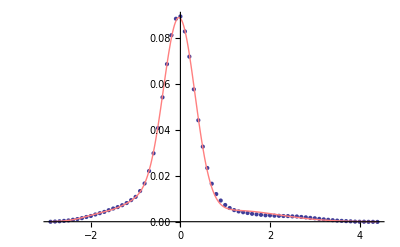

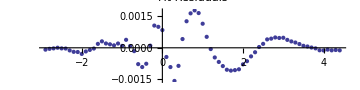

Sum of squares of residuals (as percent of total): 0.044716518108494245

Using fixed peaks analysis methods. μ -> 0.0490459

Weight | σ
0.0336051 | 0.407514
0.0668533 | -0.337783
0.800186 | 0.350643
0.0711591 | -0.509309
0.0281962 | -0.465226

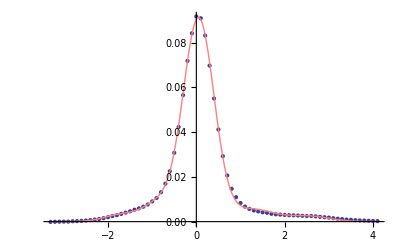

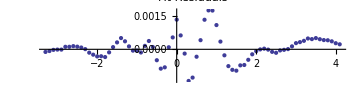

Sum of squares of residuals (as percent of total): 0.012899973079146964

Using fixed peaks analysis methods. μ -> 0.0297446

Weight | σ
0.0700059 | -0.540782
0.0474568 | -0.298535
0.796222 | -0.383076
0.0697585 | -0.508142
0.0165567 | 0.414684

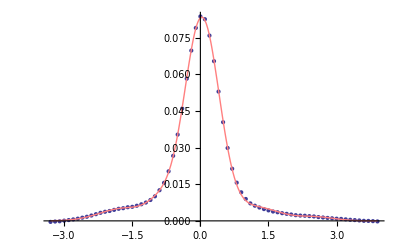

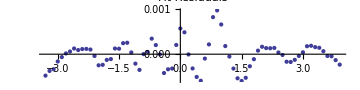

```mathematica
CSummaries=Table[FitSummary[CenteredCData[[x]],AllCModels[[x]],"g",True],{x,1,Length[CenteredCData]}];
```

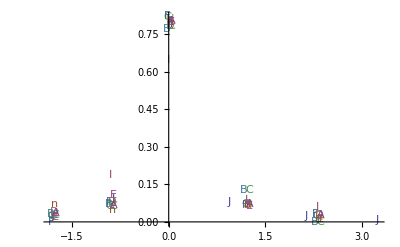

```mathematica
FixedPeaks=ComparePeaks[CSummaries,CSheets,expositions,AllCModels];
```

We can also plot based on the treatment (red = bad, green=good). There does seem to be an effect here, but we need to make sure the normalization is totally legit.

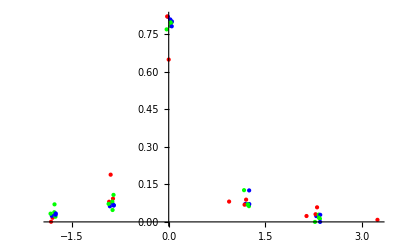

```mathematica
ListPlot[FixedPeaks,PlotStyle->StyleList]
```

#### Fitting with constrained peak positions

Recall our literature peak positions: (using 2 to account for possible peak at 2.3 or 1.9 eV)

```mathematica
Poslist={-1.8,-0.9,0,1.2,2};
```

```mathematica
Cguess={Sqrt[exweights]*0.3,Poslist,0.4+0#&/@Range[5]}ᵀ;
```

Now we’ll fit with our constrained method, giving the peaks a lot of leeway.

```mathematica
AllCModels=Model[#,Cguess,{0.9,0.9,0.9},"g",0.95,0]&/@{CenteredCData[[1]]};
```

Sum of squares of residuals (as percent of total): 0.0450505550239656

Weight | μ | σ
0.0243041 | -0.9 | 0.247235
0.0183877 | -1.36014 | 0.396141
0.896559 | 0.0328994 | 0.386128
0.0391643 | 1.832 | 0.4999
0.0215845 | 1.1 | 0.275509

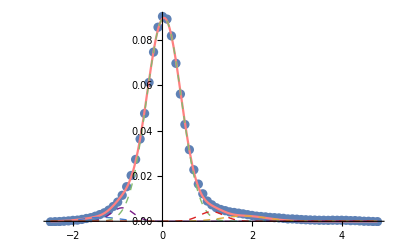

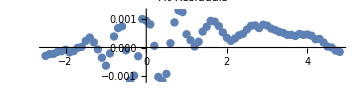

```mathematica
CSummaries=Table[FitSummary[CenteredCData[[x]],AllCModels[[x]],"g"],{x,1,1}];
```

```mathematica
ConstrainedPeaks=ComparePeaks[CSummaries,CSheets,expositions,AllCModels];
```

-Graphics-

We can also plot based on the treatment (red = bad, green=good). There does seem to be an effect here, but we need to make sure the normalization is totally legit.

```mathematica
ListPlot[FixedPeaks,PlotStyle->StyleList]
```

-Graphics-

#### Fitting with Lorentzians

We can use the “l” option in Model to fit with Lorentzians instead of Gaussians.

```mathematica
AllCModels=Model[#,guesses,"l",0.5]&/@CenteredCData;
```

The peak is too broad to be fit well by a Lorentzian, so the optimal solution is putting several smaller Lorentzians beneath it.

Sum of squares of residuals (as percent of total): 0.08197192544815889

Weight | μ | σ
0.245509 | 0.363361 | -0.268538
3.17739×10^-13 | 0.456472 | 0.753264
0.140755 | -0.406511 | -0.250401
0.323808 | 0.108796 | -0.222928
0.289928 | -0.130395 | 0.217724

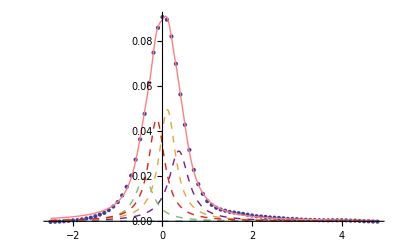

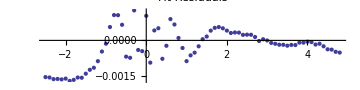

Sum of squares of residuals (as percent of total): 0.04267819806108202

Weight | μ | σ
0.0302673 | 2.38019 | -0.723259
0.05335 | -1.63315 | 0.393037
0.400197 | -0.216631 | -0.320825
0.334194 | 0.0435929 | -0.266811
0.181992 | 0.314311 | -0.268473

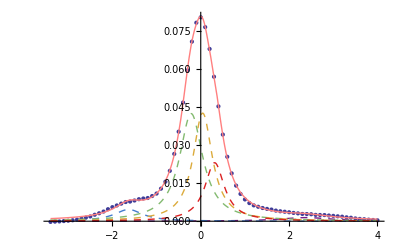

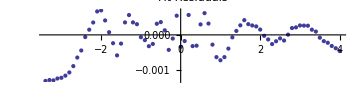

Sum of squares of residuals (as percent of total): 0.1261774484360187

Weight | μ | σ
0.650695 | -0.0988885 | 0.311235
9.68487×10^-15 | 0.788309 | 1.20283
2.76367×10^-14 | 0.173419 | -0.483618
0.349305 | 0.204504 | 0.258573
7.89775×10^-14 | 0.121405 | 0.393383

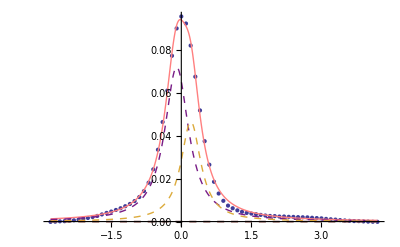

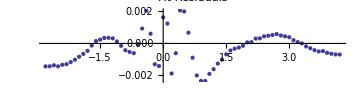

Sum of squares of residuals (as percent of total): 0.04598831826512905

Weight | μ | σ
0.317448 | -0.272109 | 0.289995
4.15719×10^-12 | 0.273476 | 0.625131
0.123322 | 0.359414 | -0.217842
0.324042 | -0.0606411 | 0.230178
0.235187 | 0.138214 | -0.209672

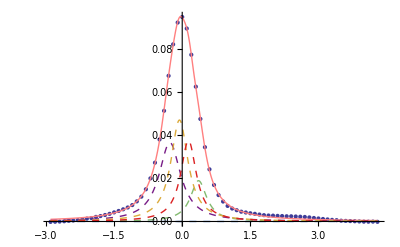

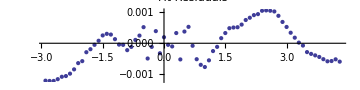

Sum of squares of residuals (as percent of total): 0.12417766265336143

Weight | μ | σ
0.32622 | 0.230394 | -0.279806
1.5272×10^-15 | -0.0526651 | 0.410713
0.265086 | -0.343372 | 0.288478
0.408694 | -0.0543698 | 0.252192
1.22499×10^-15 | -1.2061 | 0.5017

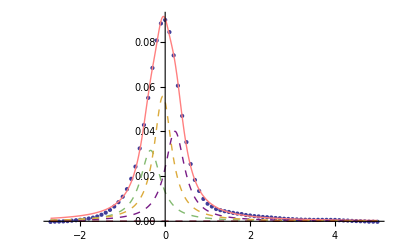

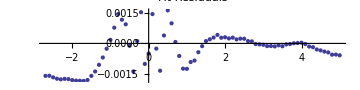

Sum of squares of residuals (as percent of total): 0.1145876503529562

Weight | μ | σ
0.460052 | -0.194925 | -0.368883
1.70172×10^-14 | -0.0258406 | 0.554008
0.187029 | 0.320493 | -0.221278
2.80111×10^-9 | 0.42662 | -8.75112×10^-9
0.352919 | 0.0569074 | 0.243326

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.05194419712994013

Weight | μ | σ
0.370293 | 0.050506 | -0.258367
0.0152027 | -1.33329 | 0.262569
0.0459128 | 0.475756 | 0.176822
0.433111 | -0.189446 | -0.321797
0.13548 | 0.269396 | -0.199778

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.06832484983751944

Weight | μ | σ
0.381788 | 0.104471 | -0.242905
1.71367×10^-11 | 0.123946 | 0.571988
8.55453×10^-12 | -0.314421 | -1.0253
0.159416 | 0.360709 | -0.221377
0.458796 | -0.149914 | -0.302534

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.12036546399674143

Weight | μ | σ
0.617562 | -0.169323 | -0.326004
5.96302×10^-13 | 0.00313191 | 0.469327
0.382438 | 0.150093 | 0.283038
8.56445×10^-17 | 0.580957 | 0.443531
5.35075×10^-15 | -1.48847 | 0.801637

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.06392435455600888

Weight | μ | σ
0.380489 | 0.114722 | -0.248496
9.68991×10^-16 | 0.356268 | 0.676162
2.66238×10^-15 | -0.586733 | -1.77525
0.481593 | -0.139425 | -0.309637
0.137918 | 0.370061 | -0.216445

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.03172786773990001

Weight | μ | σ
0.218115 | 0.213738 | -0.231421
0.341879 | -0.251588 | 0.339243
0.0211447 | -1.77293 | -0.326751
0.319481 | -0.00831279 | -0.257879
0.0993796 | 0.441475 | -0.226298

-Graphics-

-Graphics-

```mathematica
CSummaries=Table[FitSummary[CenteredCData[[x]],AllCModels[[x]],"l"],{x,1,Length[CenteredCData],1}];
```

Visualize location of peaks and weights:

```mathematica
LPeaks=ComparePeaks[CSummaries,CSheets];
```

-Graphics-

#### Fitting with Voigt functions

Similarly, we can fit with Voigt functions, which are a convolution of a Lorentzian and a Gaussian. These are commonly used when there are both broadening mechanisms present, e.g. gaussian inhomogeneity from charging or an instrument response convolved with a lifetime-limited lorentzian line. Because they are a convolution of a gaussian and a lorentzian, they have parameters characterizing both the gaussian standard deviation and the lorentzian width, so there is one more parameter. However, Voigt functions can get better results with fewer peaks, often to within a factor of two of the gaussian cases with two peaks instead of five; in this sense they are more parsimonious.

For more information on Voigt functions in fitting XPS data, see e.g. http://www.sciencedirect.com/science/article/pii/0368204894021897#

If fitting is aborted in the middle, the values of the parameters can be erroneously set and we must clear them:

```mathematica
ClearAll[A,σ,δ,μ]
```

```mathematica
AllCModels=Model[#,3,"v",0.5]&/@CenteredCData;
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize :: cvmit will be suppressed during this calculation.

NMinimize::nnum: The function value TagBox[Experimental`NumericalFunction[« 1 »], False, Rule[Editable, False]] is not a number at {A[1], A[2], A[3], δ[1], δ[2], δ[3], μ[1], μ[2], μ[3], σ[1], σ[2], σ[3]} = {0., 0.0405605, 0.322691, 2.12891, 0., 0.105667, -12.2614, 5.01088, -0.0133279, 1.2581, 0., 0.313299}.

NMinimize::nnum: The function value TagBox[Experimental`NumericalFunction[« 1 »], False, Rule[Editable, False]] is not a number at {A[1], A[2], A[3], δ[1], δ[2], δ[3], μ[1], μ[2], μ[3], σ[1], σ[2], σ[3]} = {0.131249, 0., 0.301102, 0., 0., 0.183351, 0.942911, 1.11034, 0.0406581, 0., 3.05286, 0.249363}.

```mathematica
CSummaries=Table[FitSummary[CenteredCData[[x]],AllCModels[[x]],"v"],{x,1,Length[CenteredCData],1}];
```

Sum of squares of residuals (as percent of total): 0.05214867198059576

A | μ | σ | δ
0.018968 | 1.81398 | 0.366089 | 0.33727
0.0071074 | -4.38197 | 2.78611 | 0.974859
0.973925 | 0.0277066 | 0.3015 | 0.170033

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.09371676311773312

A | μ | σ | δ
1.89586×10^-6 | -0.819873 | 0.640182 | 1.18523
0.442291 | -0.179773 | 0.824772 | 0.765853
0.557707 | -0.00324162 | 0.0012403 | 0.341475

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.0789305570181671

A | μ | σ | δ
0.0704342 | -0.527638 | 0.801493 | 0.436049
0.0342362 | -11.2437 | 4.11075 | 0.230668
0.89533 | 0.0186805 | 0.28355 | 0.135552

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.07016340285423875

A | μ | σ | δ
0.0000698937 | -7.3457 | 1.77089 | 1.69777
0.011125 | 2.49314 | 0.510716 | 0.146037
0.988805 | -0.0152923 | 0.310575 | 0.110574

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.08085052996270105

A | μ | σ | δ
6.36587×10^-12 | -4.24777 | 1.42875 | 0.359926
0. | -4.00995 | 1.86533 | 0.224486
1. | -0.0335938 | 0.326683 | 0.142298

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.00559659419557948

A | μ | σ | δ
0.120535 | -0.729592 | 0. | 0.519525
0.0994189 | 0.57173 | 0.252178 | 1.03568
0.780046 | 0.0516609 | 0.209143 | 0.222749

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.08076839356723026

A | μ | σ | δ
0.246288 | -0.181435 | 0.853161 | 0.291268
0.00621827 | -9.76588 | 5.18705 | 0.0434186
0.747494 | 0.0203431 | 0.246281 | 0.180602

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.09801758101641732

A | μ | σ | δ
0.0769518 | 0.206448 | 0.0982637 | 1.85869
1.42727×10^-6 | 0.256603 | 4.01791 | 7.32665×10^-8
0.923047 | 0.0424907 | 0.277508 | 0.151593

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.014559431682551369

A | μ | σ | δ
0.0978437 | 0.907227 | 0.0268233 | 1.31056
0.0549542 | -1.21131 | 0. | 0.476748
0.847202 | -0.0366311 | 0.227151 | 0.222839

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.003839796121129581

A | μ | σ | δ
0.0366493 | 2.48342 | 0.194756 | 0.625655
0.285629 | -0.10266 | 0. | 0.952599
0.677722 | 0.0488607 | 0.136105 | 0.26942

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.02369034459672653

A | μ | σ | δ
0.320219 | -0.177423 | 0.419201 | 1.08485
2.89289×10^-7 | -0.433707 | 1.42835 | 0.0938219
0.679781 | 0.0310113 | 0.130085 | 0.315344

-Graphics-

-Graphics-

Visualize location of peaks and weights:

```mathematica
VoigtPeaks=ComparePeaks[CSummaries,CSheets];
```

-Graphics-

```mathematica
ListPlot[VoigtPeaks,PlotStyle->StyleList]
```

-Graphics-

#### Fitting with Voigt functions with constraints

Similarly, we can fit with Voigt functions, which are a convolution of a Lorentzian and a Gaussian. These are commonly used when there are both broadening mechanisms present, e.g. gaussian inhomogeneity from charging or an instrument response convolved with a lifetime-limited lorentzian line. Because they are a convolution of a gaussian and a lorentzian, they have parameters characterizing both the gaussian standard deviation and the lorentzian width, so there is one more parameter. However, Voigt functions can get better results with fewer peaks, often to within a factor of two of the gaussian cases with two peaks instead of five; in this sense they are more parsimonious.

For more information on Voigt functions in fitting XPS data, see e.g. http://www.sciencedirect.com/science/article/pii/0368204894021897#

If fitting is aborted in the middle, the values of the parameters can be erroneously set and we must clear them:

Recall our literature peak positions: (using 2 to account for possible peak at 2.3 or 1.9 eV)

Now we’ll fit with our constrained method, giving the peaks a lot of leeway. First, tweak the parameters for just one spectrum:

```mathematica
ClearAll[A,σ,δ,μ];
CguessV={Sqrt[exweights],Poslist,0.3+0#&/@Range[5],0.3+0#&/@Range[5]}ᵀ;
Poslist={-1.8,-0.9,0,1.2,2};
AllCModels=Model[#,CguessV,{0.99,0.2,0.3,0.3},"v",0.6,0]&/@{CenteredCData[[1]]};
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
CSummaries=Table[FitSummary[CenteredCData[[x]],AllCModels[[x]],"v"],{x,1,1,1}];
```

Sum of squares of residuals (as percent of total): 0.018453781942977695

A | μ | σ | δ
0.0000765258 | -1.61611 | 0.291166 | 0.247311
0.0505834 | -0.752807 | 0.210845 | 0.355534
0.89681 | 0.0372742 | 0.229153 | 0.242717
0.0522036 | 1.3546 | 0.389619 | 0.383472
0.000326266 | 1.89473 | 0.289478 | 0.251757

-Graphics-

-Graphics-

Fit all the peaks using this method

```mathematica
ClearAll[A,σ,δ,μ];
CguessV={Sqrt[exweights],Poslist,0.3+0#&/@Range[5],0.3+0#&/@Range[5]}ᵀ;
Poslist={-1.8,-0.9,0,1.2,2.2};
AllCModels=Model[#,CguessV,{0.99,0.2,0.3,0.3},"v",0.6,0]&/@CenteredCData;
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize :: cvmit will be suppressed during this calculation.

```mathematica
CSummaries=Table[FitSummary[CenteredCData[[x]],AllCModels[[x]],"v"],{x,1,Length[CenteredCData],1}];
```

Sum of squares of residuals (as percent of total): 0.018453781942977695

A | μ | σ | δ
0.0000765258 | -1.61611 | 0.291166 | 0.247311
0.0505834 | -0.752807 | 0.210845 | 0.355534
0.89681 | 0.0372742 | 0.229153 | 0.242717
0.0522036 | 1.3546 | 0.389619 | 0.383472
0.000326266 | 1.89473 | 0.289478 | 0.251757

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.04441212142147303

A | μ | σ | δ
0.0701414 | -1.67163 | 0.346882 | 0.245159
0.0315941 | -1.08551 | 0.311061 | 0.218316
0.835453 | -0.00390998 | 0.261491 | 0.217995
0.029515 | 1.4 | 0.274757 | 0.250537
0.033297 | 2.18809 | 0.373442 | 0.383559

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.02429333598648053

A | μ | σ | δ
0.00109302 | -1.9848 | 0.211853 | 0.214162
0.0805594 | -0.997955 | 0.383132 | 0.227131
0.863856 | 0.0215462 | 0.210247 | 0.219927
0.0282088 | 1.07317 | 0.360381 | 0.272036
0.026283 | 1.8 | 0.38789 | 0.39

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.010070965305397493

A | μ | σ | δ
0.0000459651 | -1.65312 | 0.294562 | 0.328149
0.0602766 | -1.02419 | 0.238151 | 0.362134
0.874006 | -0.0126136 | 0.210056 | 0.226277
0.0330411 | 1. | 0.21 | 0.304183
0.0326308 | 2.19993 | 0.385958 | 0.389961

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.013903163072528967

A | μ | σ | δ
0.0032153 | -1.6 | 0.278412 | 0.231675
0.0612936 | -0.84365 | 0.237167 | 0.23097
0.868537 | -0.0220564 | 0.215765 | 0.251068
0.0444002 | 1.09513 | 0.3593 | 0.223902
0.0225538 | 2.11603 | 0.38776 | 0.363522

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.006251411648073411

A | μ | σ | δ
0.0000113118 | -1.99021 | 0.233251 | 0.29868
0.13376 | -0.768455 | 0.244649 | 0.372947
0.815784 | 0.0517473 | 0.215586 | 0.221544
0.0381067 | 1.02742 | 0.319889 | 0.268355
0.0123387 | 2.14634 | 0.25248 | 0.344718

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.016885660063953745

A | μ | σ | δ
0.00411434 | -1.85839 | 0.320097 | 0.340658
0.0949534 | -1.03723 | 0.387603 | 0.2338
0.832094 | 0.0209771 | 0.217068 | 0.233438
0.035756 | 1.01107 | 0.291977 | 0.216607
0.0330822 | 2.1676 | 0.349724 | 0.353914

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.02905461875157657

A | μ | σ | δ
0.0000500969 | -1.96023 | 0.356723 | 0.259434
0.0688029 | -1.00316 | 0.358373 | 0.271242
0.881232 | 0.0474411 | 0.226669 | 0.21
0.025376 | 1.02927 | 0.308385 | 0.249562
0.0245393 | 1.87766 | 0.242299 | 0.376167

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.023429049044351394

A | μ | σ | δ
0.0188803 | -1.6226 | 0.311987 | 0.272771
0.080366 | -0.881387 | 0.368118 | 0.342845
0.843167 | -0.0286257 | 0.223126 | 0.223429
0.0348039 | 1.00083 | 0.31331 | 0.252322
0.0227827 | 2.13909 | 0.212602 | 0.389317

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.01542721574248118

A | μ | σ | δ
0.0191557 | -1.64213 | 0.249212 | 0.372862
0.0503945 | -0.9599 | 0.259634 | 0.218878
0.85438 | 0.0434091 | 0.212264 | 0.228397
0.039808 | 1.01439 | 0.319743 | 0.355898
0.0362613 | 2.17323 | 0.344721 | 0.39

-Graphics-

-Graphics-

Sum of squares of residuals (as percent of total): 0.011711609554504662

A | μ | σ | δ
0.0459155 | -1.74705 | 0.3009 | 0.321622
0.0668063 | -0.823682 | 0.300447 | 0.254861
0.823594 | 0.033262 | 0.212526 | 0.260495
0.0402453 | 1.02675 | 0.284329 | 0.285475
0.0234394 | 1.99406 | 0.285757 | 0.379186

-Graphics-

-Graphics-

Visualize location of peaks and weights:

```mathematica
VoigtPeaks=ComparePeaks[CSummaries,CSheets];
```

-Graphics-

```mathematica
ListPlot[VoigtPeaks,PlotStyle->StyleList]
```

-Graphics-

#### Comparison of different fitting techniques

Here, I’ll plot the different peaks that each method produces. The position on the horizontal axis corresponds to the peak position. The position on the vertical axis corresponds to the peak weight. I will color them by surface terminated/not.

Note that there are 3 bad samples (red), 4 good samples (green), and 4 unknown samples (blue)

Completely free parameters. The bad samples definitely have a peak at 1eV that the good samples do not. This peak is typically very broad, however, so it does not seem well motivated physically.

```mathematica
ListPlot[FreePeaks,PlotStyle->StyleList]
```

-Graphics-

Peaks with better initial guesses. Again, the bad samples and two of the unknown samples have a peak at +1 eV. None of the good samples have a peak there.

```mathematica
ListPlot[HintPeaks,PlotStyle->StyleList]
```

-Graphics-

Constrained peaks. Fit is a bit worse here in general. Peaks are a little ambiguous

```mathematica
ListPlot[FixedPeaks,PlotStyle->StyleList]
```

-Graphics-

Lorentzian fitting is generally a mess because central peak is not lorentzian, so many peaks are used to fit that one.

```mathematica
ListPlot[LPeaks,PlotStyle->StyleList]
```

-Graphics-

Voigt fitting. Here, three peaks are used instead of 5/6 (which is it?). Not conclusive.

```mathematica
ListPlot[VoigtPeaks,PlotStyle->StyleList,PlotRange->{{-2,2},{0,1}}]
```

-Graphics-

### Oxygen Peak

I have not re-analyzed the oxygen peak with the latest version of the peak fitting package. For now, it makes a nice analysis exercise.

#### Setup

```mathematica
RawOData=GetSpec[XPSPath,"Excel XPS","O1s"];
```

Removing sheets that do not contain the string "O1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

{O1s Scan J,O1s Scan I,O1s Scan H,O1s Scan G,O1s Scan F,O1s Scan E,O1s Scan D,O1s Scan C,O1s Scan B,O1s Scan A,O1s Scan}

11 spectra in all.

Importing Sheet O1s Scan J

Importing Sheet O1s Scan I

Importing Sheet O1s Scan H

Importing Sheet O1s Scan G

Importing Sheet O1s Scan F

Importing Sheet O1s Scan E

Importing Sheet O1s Scan D

Importing Sheet O1s Scan C

Importing Sheet O1s Scan B

Importing Sheet O1s Scan A

Importing Sheet O1s Scan

Formatting XPS Spectra

```mathematica
OSheets=GetSheets[XPSPath,"O1s"]
```

Removing sheets that do not contain the string "O1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

11 spectra in all.

{O1s Scan J,O1s Scan I,O1s Scan H,O1s Scan G,O1s Scan F,O1s Scan E,O1s Scan D,O1s Scan C,O1s Scan B,O1s Scan A,O1s Scan}

```mathematica
Ocoordlist=CoordInit[RawOData,532.5,7,12000]
```

{{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}}}

```mathematica
PickGuesses[RawOData,Ocoordlist]
```

{,,,,,,,,,,}

```mathematica
OData=UserRemoveAve[RawOData,Ocoordlist];
```

```mathematica
CenteredOData=CenterAndNormalize/@OData;
```

#### Fitting with free parameters

Fitting works better if the fitting parameters are tweaked a little.

```mathematica
AllOModels=Model[#,4,0.7,0.1]&/@CenteredOData;
```

```mathematica
OSummaries=Table[FitSummary[CenteredOData[[x]],AllOModels[[x]]],{x,1,Length[CenteredOData]}];
```

Weights | Means | σs
0.874396 | 0. | -0.742735
0.118266 | 1.46439 | 0.505756
0.00733787 | 0.730778 | 0.202887
2.38909×10^-15 | 1.22805 | -0.0557857

-Graphics-

-Graphics-

Weights | Means | σs
0.837196 | 0. | 0.828332
0.125163 | -1.26161 | 0.513958
0.0376415 | -2.2437 | -0.524787
1.09389×10^-15 | 7.28843 | 1.13965

-Graphics-

-Graphics-

Weights | Means | σs
0.653603 | 0. | -0.884188
0.346397 | 0.357317 | -0.52724
1.05667×10^-15 | 2.5096 | 0.766575
7.45861×10^-16 | -0.23765 | 0.512961

-Graphics-

-Graphics-

Weights | Means | σs
0.776322 | 0. | -0.873546
0.209321 | 0.324272 | -0.453076
0.0110191 | -2.00676 | -0.375741
0.00333731 | 0.990021 | 0.0838162

-Graphics-

-Graphics-

Weights | Means | σs
0.534729 | 0. | 0.941181
0.348729 | 4.44663 | -0.111634
0.116542 | -0.561733 | -0.540562
7.39575×10^-14 | -1.26733 | -1.66903

-Graphics-

-Graphics-

Weights | Means | σs
0.973399 | 0. | -0.879313
0.0192061 | 0.423804 | 0.40934
0.0073945 | -1.88311 | 0.30123
2.87036×10^-15 | -3.6756 | 2.07797

-Graphics-

-Graphics-

Weights | Means | σs
0.773084 | 0. | -0.923937
0.213826 | 0.413824 | 0.482582
0.00824337 | -2.26355 | -0.406699
0.00484642 | 2.62401 | -0.40358

-Graphics-

-Graphics-

Weights | Means | σs
0.852568 | 0. | -0.806482
0.0785695 | 0.273038 | 0.385294
0.0688621 | -1.58587 | 0.637021
2.53352×10^-11 | -1.22528 | 1.09366

-Graphics-

-Graphics-

Weights | Means | σs
0.702948 | 0. | -0.919186
0.291838 | 0.446328 | 0.551286
0.00336372 | 0.48207 | -0.0744654
0.00184975 | -0.0628031 | 0.0283305

-Graphics-

-Graphics-

Weights | Means | σs
0.888669 | 0. | -0.722229
0.0680254 | -1.84434 | 0.530839
0.043306 | -1.19196 | 0.345794
1.55702×10^-15 | -0.987686 | -1.7759

-Graphics-

-Graphics-

Weights | Means | σs
0.841105 | 0. | 0.969829
0.151044 | 0.784281 | -0.489246
0.0078509 | -2.1727 | -0.36118
4.66842×10^-14 | 0.20277 | -0.484569

-Graphics-

-Graphics-

Visualize location of peaks and weights:

```mathematica
ComparePeaks[OSummaries,OSheets]
```

-Graphics-

#### Fitting with fixed peak positions

Fitting works better if the fitting parameters are tweaked a little.

```mathematica
AllOModels=Model[#,4,0.7,0.1]&/@CenteredOData;
```

```mathematica
OSummaries=Table[FitSummary[CenteredOData[[x]],AllOModels[[x]]],{x,1,Length[CenteredOData]}];
```

Weights | Means | σs
0.874396 | 0. | -0.742735
0.118266 | 1.46439 | 0.505756
0.00733787 | 0.730778 | 0.202887
2.38909×10^-15 | 1.22805 | -0.0557857

-Graphics-

-Graphics-

Weights | Means | σs
0.837196 | 0. | 0.828332
0.125163 | -1.26161 | 0.513958
0.0376415 | -2.2437 | -0.524787
1.09389×10^-15 | 7.28843 | 1.13965

-Graphics-

-Graphics-

Weights | Means | σs
0.653603 | 0. | -0.884188
0.346397 | 0.357317 | -0.52724
1.05667×10^-15 | 2.5096 | 0.766575
7.45861×10^-16 | -0.23765 | 0.512961

-Graphics-

-Graphics-

Weights | Means | σs
0.776322 | 0. | -0.873546
0.209321 | 0.324272 | -0.453076
0.0110191 | -2.00676 | -0.375741
0.00333731 | 0.990021 | 0.0838162

-Graphics-

-Graphics-

Weights | Means | σs
0.534729 | 0. | 0.941181
0.348729 | 4.44663 | -0.111634
0.116542 | -0.561733 | -0.540562
7.39575×10^-14 | -1.26733 | -1.66903

-Graphics-

-Graphics-

Weights | Means | σs
0.973399 | 0. | -0.879313
0.0192061 | 0.423804 | 0.40934
0.0073945 | -1.88311 | 0.30123
2.87036×10^-15 | -3.6756 | 2.07797

-Graphics-

-Graphics-

Weights | Means | σs
0.773084 | 0. | -0.923937
0.213826 | 0.413824 | 0.482582
0.00824337 | -2.26355 | -0.406699
0.00484642 | 2.62401 | -0.40358

-Graphics-

-Graphics-

Weights | Means | σs
0.852568 | 0. | -0.806482
0.0785695 | 0.273038 | 0.385294
0.0688621 | -1.58587 | 0.637021
2.53352×10^-11 | -1.22528 | 1.09366

-Graphics-

-Graphics-

Weights | Means | σs
0.702948 | 0. | -0.919186
0.291838 | 0.446328 | 0.551286
0.00336372 | 0.48207 | -0.0744654
0.00184975 | -0.0628031 | 0.0283305

-Graphics-

-Graphics-

Weights | Means | σs
0.888669 | 0. | -0.722229
0.0680254 | -1.84434 | 0.530839
0.043306 | -1.19196 | 0.345794
1.55702×10^-15 | -0.987686 | -1.7759

-Graphics-

-Graphics-

Weights | Means | σs
0.841105 | 0. | 0.969829
0.151044 | 0.784281 | -0.489246
0.0078509 | -2.1727 | -0.36118
4.66842×10^-14 | 0.20277 | -0.484569

-Graphics-

-Graphics-

Visualize location of peaks and weights:

```mathematica
ComparePeaks[OSummaries,OSheets]
```

-Graphics-

### Conclusions and Analysis

In general, performing a multi-gaussian fit with all of the free parameters fails to capture the underlying physics of multiple species contributing to a single line.

When there are no artificial constraints on the parameters, the best fit typically involves a central peak plus a smaller, broader peak to fit the tails of the energy distribution. However, this is unsatisfying on physical grounds, because we do not expect a second species to exist at the same energy value with much more broadening. A factor of 3-10 worse fit is obtained when constraining the peaks to lie at literature values. In this case, the linewidths are all similar as we would expect.

The conclusion just from fitting gaussians is that the gaussian function is a poor model for even the single-peak physics. Similar conclusions hold with lorentzians, except here the lorentzians are too narrow (but have nice fat tails), so several similar lorentzians are clustered very close together to simulate the larger peak. Fitting with Voigt functions seems to be a logical, parsimonious, and popular choice. Refining the fitting routine by constraining the peaks gives excellent results.